DVOJITÁ GEOMETRICKÁ TRANSFORMÁCIA BODU

==========================================

POČIATOČNÝ BOD:

Súradnice bodu P:

P = (1/2
-5/3)

Vlastnosti bodu:

Vzdialenosť od počiatku: 10

Kvadrant: IV

PRVÁ TRANSFORMÁCIA: Posun

GEOMETRICKÉ TRANSFORMÁCIE BODU - POSUN

========================================

ZADANIE:

Majme bod P so súradnicami:

(1/2
-5/3)

Vykonajte posun bodu v 2D priestore pomocou vektora posunu: Δ = [-6, -3]

Transformačná matica posunu v homogénnych súradniciach:

(1 | 0 | -6
0 | 1 | -3
0 | 0 | 1)

POSTUP:

Pre výpočet použijeme maticu posunu v homogénnych súradniciach:

Transformačná matica:

(1 | 0 | dx
0 | 1 | dy
0 | 0 | 1)

Pre naše hodnoty:

dx = -6

dy = -3

Posun vykonáme pomocou vzorcov:

x' = x + dx

y' = y + dy

Výpočet pre bod P:

Pôvodné súradnice: [1/2, -5/3]

Výpočet x-ovej súradnice:

x' = x + dx = 1/2 + -6

x' = -11/2

Výpočet y-ovej súradnice:

y' = y + dy = -5/3 + -3

y' = -14/3

Overenie pomocou inverznej transformácie:

x = x' + (-dx) = -11/2 + (6) = 1/2

y = y' + (-dy) = -14/3 + (3) = -5/3

Maticový zápis:

(1 | 0 | -6
0 | 1 | -3
0 | 0 | 1) · (1/2
-5/3
1) = (-11/2
-14/3
1)

VÝSLEDOK:

Súradnice bodu po posune:

(-11/2
-14/3)

VIZUALIZÁCIA:

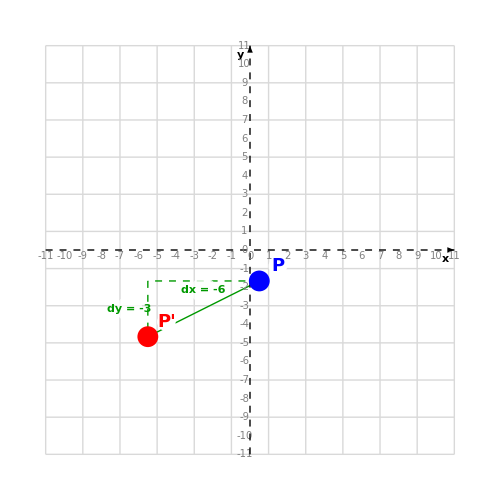

LEGENDA:

• Modrý bod: Pôvodný bod P

• Červený bod: Posunutý bod P'

• Zelená šípka: Vektor posunu

• Zelené prerušované čiary: Posun po súradniciach

• Mriežka: Súradnicový systém

Pôvodný bod (modrá):

Bod P: {1/2,-5/3}

Výsledný bod (červená):

Bod P': {-11/2,-14/3}

Inverzná transformácia:

Pre vrátenie do pôvodného stavu použite vektor posunu:

Δ' = [6, 3] (opačný vektor)

DRUHÁ TRANSFORMÁCIA: Rotácia

GEOMETRICKÉ TRANSFORMÁCIE BODU - ROTÁCIA

========================================

ZADANIE:

Majme bod P so súradnicami:

P = (-11/2
-14/3)

Vykonajte rotáciu bodu v 2D priestore okolo počiatku súradnicovej sústavy [0,0] o uhol α = 60°.

Transformačná matica rotácie:

(1/2 | -(√3)/2
(√3)/2 | 1/2)

POSTUP:

Pre výpočet použijeme maticu rotácie:

Transformačná matica:

(cos(α) | -sin(α)
sin(α) | cos(α))

Naša hodnotu α = 60°:

cos(α) = 1/2

sin(α) = √3/2

Rotáciu vykonáme pomocou vzorcov:

x' = x · cos(α) - y · sin(α)

y' = x · sin(α) + y · cos(α)

Výpočet pre bod P:

Pôvodné súradnice: [-11/2, -14/3]

Výpočet x-ovej súradnice:

x' = x · cos(α) - y · sin(α)

x' = -11/2 · 1/2 - -14/3 · √3/2

x' = -11/4 + 7/√3

x' = -11/4 + 7/√3

Výpočet y-ovej súradnice:

y' = x · sin(α) + y · cos(α)

y' = -11/2 · √3/2 + -14/3 · 1/2

y' = -7/3 - (11 · √3)/4

y' = -7/3 - (11 · √3)/4

Výsledné súradnice: [-11/4 + 7/√3, -7/3 - (11 · √3)/4]

Overenie pomocou inverznej transformácie:

Pre inverzný uhol α' = -60°:

cos(α') = 1/2

sin(α') = -1/2 · √3

x = x' · cos(α') - y' · sin(α')

x = -11/4 + 7/√3 · 1/2 - -7/3 - (11 · √3)/4 · -1/2 · √3

x = -11/2

x = -11/2 = -11/2

y = x' · sin(α') + y' · cos(α')

y = -11/4 + 7/√3 · -1/2 · √3 + -7/3 - (11 · √3)/4 · 1/2

y = -14/3

y = -14/3 = -14/3

Maticový zápis:

(1/2 | -(√3)/2
(√3)/2 | 1/2) · (-11/2
-14/3) = (-11/4+7/(√3)
-7/3-(11 √3)/4)

VÝSLEDOK:

Súradnice bodu po rotácii:

P' = (-11/4+7/(√3)
-7/3-(11 √3)/4)

VIZUALIZÁCIA:

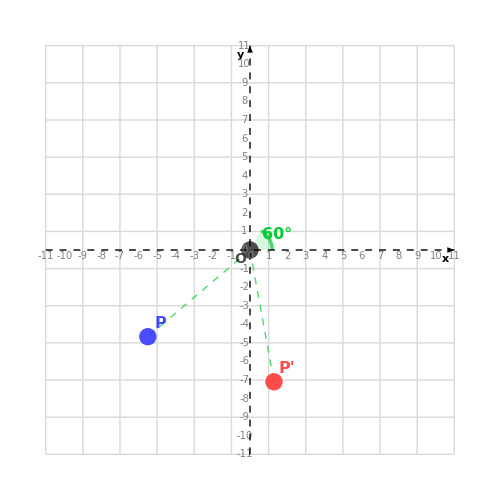

LEGENDA:

• Modrý bod: Pôvodný bod P

• Červený bod: Otočený bod P'

• Zelený oblúk: Znázornenie uhlu rotácie

• Zelené prerušované čiary: Spojenia bodov s počiatkom

• Mriežka: Súradnicový systém

• O: Počiatok súradnicovej sústavy - stred rotácie

Pôvodné súradnice (modrá):

Bod P: {-11/2,-14/3}

Výsledné súradnice (červená):

Bod P': {-11/4+7/(√3),-7/3-(11 √3)/4}

Inverzná transformácia:

Pre vrátenie do pôvodného stavu použite rotáciu o opačný uhol:

α' = -α = -60°

MATEMATICKÉ VLASTNOSTI:

• Rotácia okolo počiatku zachováva vzdialenosť bodu od počiatku sústavy [0,0]

• Rotácia je izometrická transformácia - zachováva vzdialenosti

• Rotácia zachováva uhly medzi úsečkami a ich dĺžky

• Počiatok súradnicovej sústavy [0,0] je fixný bod rotácie - zostáva nezmenený

• Ak bod P leží na kruhu so stredom v počiatku, po rotácii zostáva na tom istom kruhu

TABUĽKA ŠPECIÁLNYCH HODNÔT:

Hodnoty pre najčastejšie uhly:

α | sin(α) | cos(α)
0° | 0 | 1
30° | 1/2 | √3/2
45° | 1/√2 | 1/√2
60° | √3/2 | 1/2
90° | 1 | 0
120° | √3/2 | -1/2
135° | 1/√2 | -1/√2
150° | 1/2 | -√3/2
180° | 0 | -1
270° | -1 | 0
360° | 0 | 1

POSTUPNÝ VÝPOČET:

Pôvodný bod P:

Súradnice:

{1/2,-5/3}

Vlastnosti bodu:

Vzdialenosť od počiatku: 10

Kvadrant: IV

Po prvej transformácii (Posun):

Súradnice bodu P':

{-11/2,-14/3}

Vlastnosti bodu:

Vzdialenosť od počiatku: 10

Kvadrant: III

Po druhej transformácii (Rotácia):

Súradnice bodu P'':

{-11/4+7/(√3),-7/3-(11 √3)/4}

Vlastnosti bodu:

Vzdialenosť od počiatku: 10

Kvadrant: IV

SÚHRNNÁ VIZUALIZÁCIA:

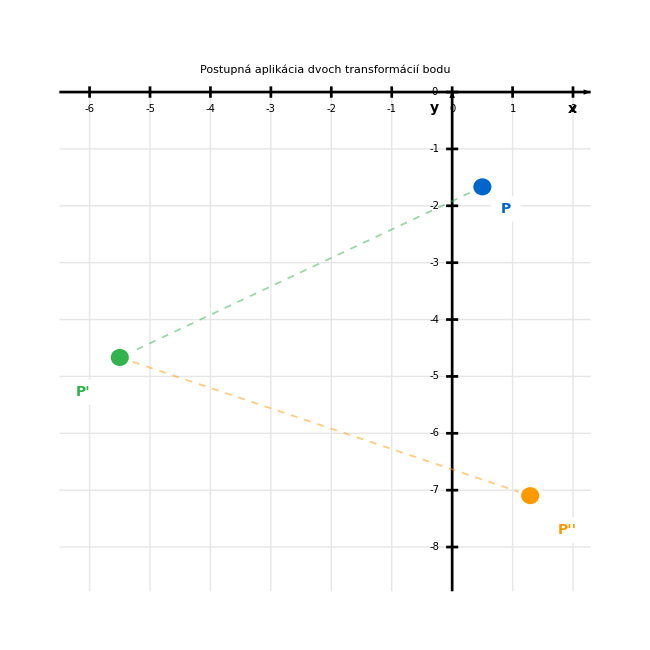

LEGENDA:

• Modré body: Pôvodný bod P

• Tmavozelené body: Bod P' po prvej transformácii (Posun)

• Oranžové body: Bod P'' po druhej transformácii (Rotácia)

Postupnosť transformácií:

1. Posun

2. Rotácia

{{1/2,-5/3},{-11/2,-14/3},{-11/4+7/(√3),-7/3-(11 √3)/4},Posun,Rotácia}

```mathematica
BodDvojitaTransformacia[]
```